```mathematica
(*plot in color*)
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(*plot in grayscale*)
colors={RGBColor[0.3,0.3,0.3],RGBColor[0.4,0.4,0.4],RGBColor[0.6,0.6,0.6]}
```

{RGBColor[0.3, 0.3, 0.3],RGBColor[0.4, 0.4, 0.4],RGBColor[0.6, 0.6, 0.6]}

```mathematica
(*font sizes*)
fontTicks=18;
fontAxesLabel=24;
fontAnnotations=22;
```

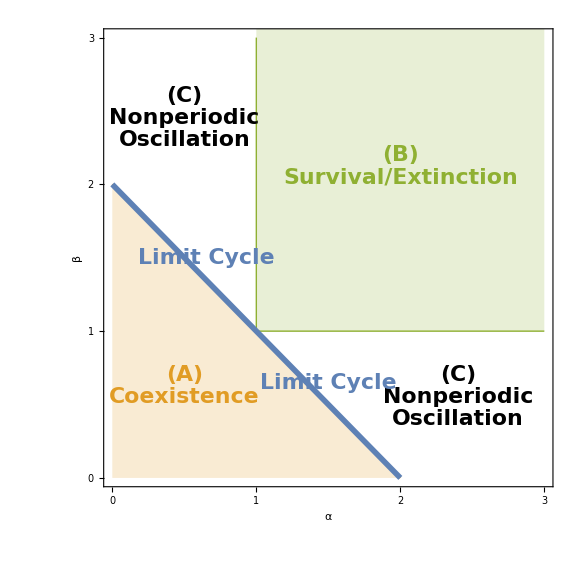

```mathematica
(*lines and shading*)
p1=Plot[2-alpha,{alpha,0,2},PlotStyle->colors[[2]],Filling->Axis,PlotRange->{{0,3},{0,3}},ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->{{0,1,2,3},{0,1,2,3}},FrameTicksStyle->Directive[fontTicks,FontFamily->"Latin Modern Sans"],FrameLabel->{"α","β"},LabelStyle->Directive[fontAxesLabel,FontFamily->"Latin Modern Math"],RotateLabel->False];
p2=Plot[1,{alpha,1,3},PlotStyle->{Thick,colors[[3]]}];
p3=Graphics[{Thick,colors[[3]],Line[{{1,1},{1,3}}]}];
p4=Plot[4,{alpha,1,3},PlotStyle->colors[[3]],Filling->1];
p5=Plot[2-alpha,{alpha,0,2},PlotStyle->{Thickness[0.007],colors[[1]]}];

(*text annotations*)
t1a=Graphics[Text[Style["(A)",Bold,fontAnnotations,colors[[2]]],{0.5,0.7}]];
t1b=Graphics[Text[Style["Coexistence",Bold,fontAnnotations,colors[[2]]],{0.5,0.55}]];
t2a=Graphics[Text[Style["(B)",Bold,fontAnnotations,colors[[3]]],{2,2.2}]];
t2b=Graphics[Text[Style["Survival/Extinction",Bold,fontAnnotations,colors[[3]]],{2,2.05}]];
t3a=Graphics[Text[Style["(C)",Bold,fontAnnotations],{0.5,2.6}]];
t3b=Graphics[Text[Style["Nonperiodic",Bold,fontAnnotations],{0.5,2.45}]];
t3c=Graphics[Text[Style["Oscillation",Bold,fontAnnotations],{0.5,2.3}]];
t4a=Graphics[Text[Style["(C)",Bold,fontAnnotations],{2.4,0.7}]];
t4b=Graphics[Text[Style["Nonperiodic",Bold,fontAnnotations],{2.4,0.55}]];
t4c=Graphics[Text[Style["Oscillation",Bold,fontAnnotations],{2.4,0.4}]];
t5a=Graphics[Text[Style["Limit Cycle",Bold,fontAnnotations,colors[[1]]],{1.5,0.65},Automatic,{1,-1}]];
t5b=Graphics[Text[Style["Limit Cycle",Bold,fontAnnotations,colors[[1]]],{0.65,1.5},Automatic,{1,-1}]];

(*show all curves and annotations in a single figure*)
Show[p1,p2,p3,p4,p5,t1a,t1b,t2a,t2b,t3a,t3b,t3c,t4a,t4b,t4c,t5a,t5b]
```